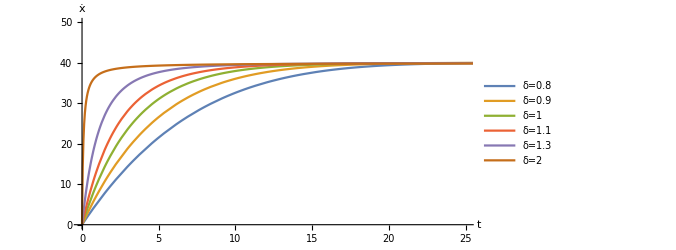

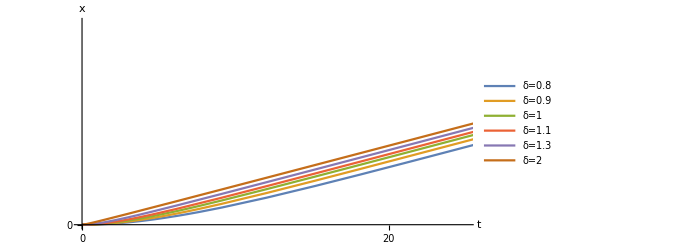

```mathematica
speed =Module[{e},
tt=150;
tmax =150;
Subscript[V, max] =40;
vm=0;

R[t_] := If[t <= tt, 1,0];
RR[t_] := If[t <= tt, 0,1];

solF1= NDSolve[{u1''[t]== R[t]*a*(Power[Subscript[V, max]-u1'[t],0.8]), u1[t /; t≤ 0] == -0*λ, u1'[t /; t≤ 0] == 0},u1,{t,0 ,tmax}];
solF2= NDSolve[{u2''[t]== R[t]*a*(Power[Subscript[V, max]-u2'[t],0.9]), u2[t /; t≤ 0] == -0*λ, u2'[t /; t≤ 0] == 0},u2,{t,0 ,tmax}];
solF3= NDSolve[{u3''[t]== R[t]*a*(Power[Subscript[V, max]-u3'[t],1]), u3[t /; t≤ 0] == -0*λ, u3'[t /; t≤ 0] == 0},u3,{t,0 ,tmax}];
solF4= NDSolve[{u4''[t]== R[t]*a*(Power[Subscript[V, max]-u4'[t],1.1]), u4[t /; t≤ 0] == -0*λ, u4'[t /; t≤ 0] == 0},u4,{t,0 ,tmax}];
solF5= NDSolve[{u5''[t]== R[t]*a*(Power[Subscript[V, max]-u5'[t],1.3]), u5[t /; t≤ 0] == -0*λ, u5'[t /; t≤ 0] == 0},u5,{t,0 ,tmax}];
solF6= NDSolve[{u6''[t]== R[t]*a*(Power[Subscript[V, max]-u6'[t],2]), u6[t /; t≤ 0] == -0*λ, u6'[t /; t≤ 0] == 0},u6,{t,0 ,tmax}];
ParametricPlot[{Evaluate[{t,u1'[t]/4} /. solF1],Evaluate[{t,u2'[t]/4} /. solF2],Evaluate[{t,u3'[t]/4} /. solF3],Evaluate[{t,u4'[t]/4} /. solF4],Evaluate[{t,u5'[t]/4} /. solF5],Evaluate[{t,u6'[t]/4} /. solF6]},{t,0,tmax},PlotStyle->{Automatic,Automatic,Automatic,Automatic,Automatic}, PlotRange->{{0,25},{0,12.5}},AxesLabel->{Style[t,15],Style[ẋ,15]},FormatType->StandardForm,PlotLegends->Placed[{"δ=0.8","δ=0.9",Style["δ=1",Bold],"δ=1.1","δ=1.3","δ=2"},{Right,Center}],ImageSize->500,Ticks->{{{0,0},{5,5},{10,10},{15,15},{20,20},{25,25}},{{0,0},{2.5,10},{5,20},{7.5,30},{10,40},{12.5,50}}},
TicksStyle->Directive[Automatic,15]]
]
path =Module[{e},
tt=150;
tmax =150;
Subscript[V, max] =40;
vm=0;

R[t_] := If[t <= tt, 1,0];
RR[t_] := If[t <= tt, 0,1];

solF1= NDSolve[{u1''[t]== R[t]*a*(Power[Subscript[V, max]-u1'[t],0.8]), u1[t /; t≤ 0] == -0*λ, u1'[t /; t≤ 0] == 0},u1,{t,0 ,tmax}];
solF2= NDSolve[{u2''[t]== R[t]*a*(Power[Subscript[V, max]-u2'[t],0.9]), u2[t /; t≤ 0] == -0*λ, u2'[t /; t≤ 0] == 0},u2,{t,0 ,tmax}];
solF3= NDSolve[{u3''[t]== R[t]*a*(Power[Subscript[V, max]-u3'[t],1]), u3[t /; t≤ 0] == -0*λ, u3'[t /; t≤ 0] == 0},u3,{t,0 ,tmax}];
solF4= NDSolve[{u4''[t]== R[t]*a*(Power[Subscript[V, max]-u4'[t],1.1]), u4[t /; t≤ 0] == -0*λ, u4'[t /; t≤ 0] == 0},u4,{t,0 ,tmax}];
solF5= NDSolve[{u5''[t]== R[t]*a*(Power[Subscript[V, max]-u5'[t],1.3]), u5[t /; t≤ 0] == -0*λ, u5'[t /; t≤ 0] == 0},u5,{t,0 ,tmax}];
solF6= NDSolve[{u6''[t]== R[t]*a*(Power[Subscript[V, max]-u6'[t],2]), u6[t /; t≤ 0] == -0*λ, u6'[t /; t≤ 0] == 0},u6,{t,0 ,tmax}];
ParametricPlot[{Evaluate[{t,u1[t]/(40*4)} /. solF1],Evaluate[{t,u2[t]/(40*4)} /. solF2],Evaluate[{t,u3[t]/(40*4)} /. solF3],Evaluate[{t,u4[t]/(40*4)} /. solF4],Evaluate[{t,u5[t]/(40*4)} /. solF5],Evaluate[{t,u6[t]/(40*4)} /. solF6]},{t,0,tmax},PlotStyle->{Automatic,Automatic,Automatic,Automatic,Automatic}, PlotRange->{{0,25},{0,12.5}},AxesLabel->{Style[t,15],Style[x,15]},FormatType->StandardForm,PlotLegends->Placed[{"δ=0.8","δ=0.9",Style["δ=1",Bold],"δ=1.1","δ=1.3","δ=2"},{Left,Center}],ImageSize->500,Ticks->{{0,20,40,60,80,100},{{0,0},{10,400},{20,800},{30,1200},{40,1600},{50,2000},{60,2400},{80,3200},{100,4000}}},TicksStyle->Directive[Automatic,15]]
]
```